```mathematica
Quit[]
```

```mathematica
rawdata =Import["/Users/stevenschowalter/Desktop/phys191mms/HeData/mms_He_312run7.txt","Table"];
```

```mathematica
num=Dimensions[rawdata][[1]]
```

15255

```mathematica
time=Take[rawdata,All,{3}];
voltage=Take[rawdata,All,{2}];
pulse=Take[rawdata,All,{1}];
```

```mathematica
temp=Table[0,{i,num}];
```

```mathematica
Do[temp[[i]]=ⅇ^(.0578*Log[voltage[[i]]]^8+.4845*Log[voltage[[i]]]^7+1.593*Log[voltage[[i]]]^6+2.521*Log[voltage[[i]]]^5+1.813*Log[voltage[[i]]]^4+.2846*Log[voltage[[i]]]^3-.1635*Log[voltage[[i]]]^2-.3503Log[voltage[[i]]]+.6568),{i,1,num}];
```

```mathematica
timetemp=Table[0,{i,num}];
Do[timetemp[[i]]=Flatten[{time[[i]],temp[[i]]},2],{i,1,num}]
```

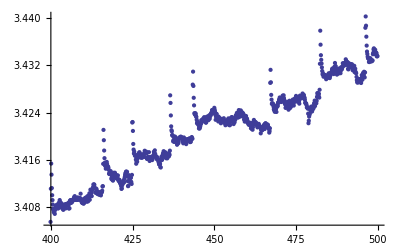

```mathematica
ListPlot[Take[timetemp,{4000,5000}]]
```

```mathematica
Q=10.5^2/1116 10^-2;
```

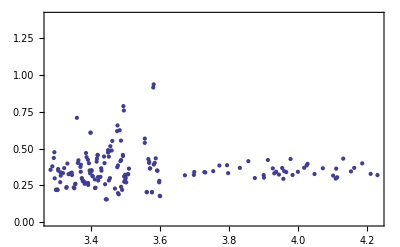

```mathematica
threshold=.006;
threshold2=.01;
dT={};
Do[If[temp[[i+2]][[1]]>temp[[i]][[1]]+threshold,{dT=Join[dT,{{temp[[i]][[1]],Q/(-Mean[Take[temp,{i-10,i-2}]][[1]]+Mean[Take[temp,{i+20,i+25}]][[1]])}}]}],{i,11,7000}]
Do[If[temp[[i+2]][[1]]>temp[[i]][[1]]+threshold,{dT=Join[dT,{{temp[[i]][[1]],Q/(-Mean[Take[temp,{i-10,i-2}]][[1]]+Mean[Take[temp,{i+20,i+25}]][[1]])}}]}],{i,8500,10000}]
Do[If[temp[[i+1]][[1]]>temp[[i]][[1]]+threshold2,{dT=Join[dT,{{temp[[i]][[1]],Q*10/(-Mean[Take[temp,{i-10,i-3}]][[1]]+Mean[Take[temp,{i+30,i+50}]][[1]])}}]}],{i,11500,15150}]
ListPlot[dT,PlotRange->{0,1.4},Frame->True,Axes->False]
```

```mathematica
dV=Take[dT,All,{2}];
V=Take[dT,All,{1}];
```

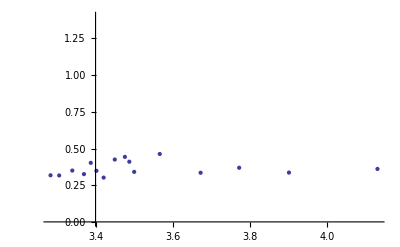

```mathematica
avgsize=10;
avgnum=Quotient[171,avgsize];
avgV=Take[V,{1,-1,avgsize}];
avgdV=Table[0,{i,avgnum}];
Do[avgdV[[i]]=Mean[Take[dV,{1+avgsize(i-1),avgsize(i)}]],{i,1,avgnum}]
avgdT=Table[0,{i,avgnum}];
Do[avgdT[[i]]=Flatten[{avgV[[i]],avgdV[[i]]},2],{i,1,avgnum}]
ListPlot[avgdT,PlotRange->{0,1.4},Joined->False]
```

```mathematica
avgdT;
```

```mathematica
avgnum
```

17

```mathematica
Dimensions[dT]
```

{171,2}

```mathematica
avgdT
```

{{3.28329,0.317645},{3.30569,0.316468},{3.33966,0.349815},{3.36992,0.325512},{3.3876,0.402453},{3.40228,0.348124},{3.42091,0.301899},{3.4498,0.425055},{3.47605,0.443187},{3.48753,0.410121},{3.50012,0.340973},{3.56646,0.462857},{3.58236,-0.685447},{3.67235,0.334939},{3.7723,0.368975},{3.90139,0.336145},{4.13083,0.360907}}

```mathematica
Dimensions[avgdT]
```

{17,2}

```mathematica
normavgdT=Table[0,{i,17}];
```

```mathematica
Do[normavgdT[[i]]={Take[avgdT[[i]],{1}][[1]],Take[avgdT[[i]],{2}][[1]]-(0.015932467940417003*Take[avgdT[[i]],{1}][[1]]+0.0012545580454563976*(Take[avgdT[[i]],{1}][[1]])^3)},{i,1,17}]
```

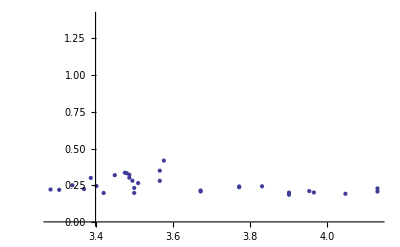

```mathematica
ListPlot[normavgdT,PlotRange->{0,1.4}]
```

```mathematica
Take[avgdT[[1]],{2}][[1]]
```

0.317645

```mathematica
finalC=Table[1,{i,17}];
Do[finalC[[i]]={normavgdT[[i]][[1]],(1/25.4)/(.0005385)normavgdT[[i]][[2]]},{i,1,17}]
```

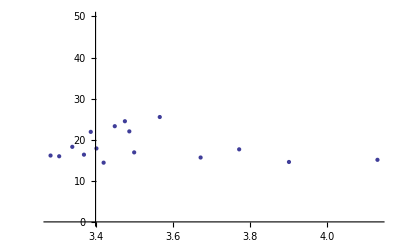

```mathematica
ListPlot[finalC,PlotRange->{0,50}]
```